Theory

#### Vector spaces

#### Subsubsection. Force vector

The force acts in the direction
								 OverHat[F̲](θ_0)=-cos(θ_0) (e̲)_1+sin(θ_0) (e̲)_2,
where θ_0∈[0,π]. We are going to say that we cannot peel the film at angles at greater than π or less than 0. This is something we are simply going to assume, even though at ceratin a values we might be able to pull in directions with θ_0<0 and θ_0>π.

#### Subsubsection. Tangent Vector

We  define the tangent  to the surface as

T̲(s):=(d r̲)/(d s)
=d/(d s) (x (s)"e_1"+ y(s)"e_2")
Let's say that x=s,  then x(s)=s, y(s)=f(s), and we get  T̲(s)="e_1"+f'(s)"e_2", or alternately, as T̲(x)="e_1"+f'(x)"e_2". We define OverHat[T̲](x):=("e_1"+f'(x)"e_2")/(1+f'(x)^2)^(1/2), where by (·)^(1/2): ℝ_(≥ 0)→ℝ_(≥ 0) is the   positive square root function.

#### Subsubsection. Rotation tensor

Orth^+ is the set of all rotation operators on  𝔼.
The expression R[θ, e̲] , where  R̲: (-π, π] × 𝔼 -> (Orth^+),  
denotes a linear operator on 𝔼  that rotates a vector about the vector e̲ in the counter clockwise direction by x radians. For examples, for example R[θ,

R̲(θ,(e̲)_3)=cos(θ)(e̲)_1⊗ (e̲)_1+sin(θ) (e̲)_2⊗ (e̲)_1+cos(θ)(e̲)_2⊗(e̲)_2-sin(θ)(e̲)_1⊗(e̲)_2

#### Subsubsection. Effective peeling angle

ψ_hk∈(-π,  π] is defined such that 
R[ψ_hk].OverHat[F̲][θ_0]=-OverHat[T̲](x) or equivalently
R[-ψ_hk].-OverHat[T̲](x)=OverHat[F̲][θ_0],

For no local penetration it is required that 0≤  ψ_hk ≤  π. For penetration the condition is -π<  ψ_hk <  0.

#### Subsubsection. Hello

#### Subsubsection Tangent angle

The tangent angle at the location x is the unique number 
θ_t(x)∈(-π,  π]  such that
 R[θ_t(x)].(e̲)_1= OverHat[T̲](x). 
Since we represent the surface as a function, it can be shown that  θ_t(x)  in fact ∈(-π/2,  π/2).

#### Subsubsection Max and min angle

We know that 
 			ψ_hk = θ_0+θ_t[𝒻,a].----------(*)
 
 (Numerical proof done)

Cos[ψ_hk-θ_0]=Cos[θ_t](follows from *)
Sin[ψ_hk-θ_0]=Sin[θ_t] (also follows *)
Tan[ψ_hk - θ_0]=Tan[θ_t] (follows from previous two equations)


hat are the limits on no penetration

Rotation (in the counter clock wise direction) of F

Calculations

```mathematica
Off[Unset::norep];
Names@{"Global`*","ComplexSymbols`*"};
ClearAll[#] & /@(%);
Remove[#] &/@(%%);
```

```mathematica
<<Notation`
Symbolize[UnderBar[x_]]
Symbolize[OverHat[x_]]
Symbolize[Subscript[x_, y_]]
```

```mathematica
ProblemHK="WavyPeeling`";
Module[{x},x=ToExpression[ProblemHK~~"sympaltte"];
If[ValueQ[x],NotebookClose[x]]];
Quiet[Remove[#] ]& /@ {ProblemHK~~"*"};
Begin["WavyPeeling`"];
If[ValueQ[sympaltte],NotebookClose[sympaltte]];
Quiet[ClearAll[#] ]& /@ {ProblemHK~~"*"};
Get[URLDownload["https://raw.githubusercontent.com/haneeshk/ForBetterMMAExperience/master/ComplexSymbols.wl"]];
syms=AssignLabels[{"e_1","e_2","e_3","u","∇u","f'_min","f'_max","(a, f(a))","λ","μ","I","n_sd","^1u","^2u","^3u"}];
sympaltte=SymbolPalette["syms",syms,1];
"n_sd"=3;
"I"=Table[KroneckerDelta[i,j],{i,1,"n_sd"},{j,1,"n_sd"}];

End[];
AppendTo[$ContextPath, "SphereTranslation`"];
$ContextPath=DeleteDuplicates[$ContextPath];
```

Complex Symbols Package Loaded

```mathematica
pltStyles=;
(*AspectRatio->1/Subscript[a, max],*)

a::usage="Interface delamination length";
Subscript[e̲, 1]::usage="Basis vector for 𝔼";
Subscript[e̲, 2]::usage="Basis vector for 𝔼";
Subscript[e̲, 1]:={1,0};
Subscript[e̲, 2]:={0,1};
ϱ[x_]=(Sin[2π x]+1/(√3) Sin[4π x]);
NMaxValue[{ϱ[x],0≤ x≤1},x];
ϱ[x_]=1/Evaluate[%] ϱ[x];
f[λ_,A_]:=Function[{a}, A λ ϱ[a/λ] ]
OverHat[F̲][Subscript[θ, 0]:_]:= -Cos[Subscript[θ, 0]] Subscript[e̲, 1]+Sin[Subscript[θ, 0]] Subscript[e̲, 2];
T̲[𝒻_,a_]:=Subscript[e̲, 1]+𝒻'[a] Subscript[e̲, 2];
OverHat[T̲][𝒻_,a_]:=(T̲[𝒻,a])/((1+𝒻'[a]^2)^(1/2));
Subscript[l, p][𝒻_,a_]:=NIntegrate[(1+𝒻'[x]^2)^(1/2),{x,0,a}];

Subscript[ψ, wd][Subscript[θ, 0]:_,𝒻_,a_]:=Subscript[θ, 0]+ArcTan[𝒻'[a]];

Subscript[ψ, hk][Subscript[θ, 0]:_,𝒻_,a_]:=Module[{sol,θ},
sol=Solve[{(#==0),-π< θ≤  π},θ]&/@Flatten[RotationMatrix[θ].OverHat[F̲][Subscript[θ, 0]]+OverHat[T̲][𝒻,a]];
Return[(Intersection@@Round[θ/.sol,10^-5])[[1]]//N];
Remove[θ,sol];

]

ClearAll[Subscript[θ, t]];
Subscript[θ, t][𝒻_,a_]:=Module[{θ},
sol=Solve[{(#==0),-π/2< θ < π/2},θ]&/@Flatten[RotationMatrix[θ].Subscript[e̲, 1]-OverHat[T̲][𝒻,a]];
Return[Apply[Intersection,Round[θ/.sol,10^-10]][[1]]];
Remove[θ]
]
```

```mathematica
ClearAll[check]
check[a_]:=Module[{Subscript[θ, 0]=π/3,A=0.5,λ=1,𝒻},
𝒻=f[λ,A];
Return[{Subscript[ψ, wd][Subscript[θ, 0],𝒻,a],Subscript[ψ, hk][Subscript[θ, 0],f[λ,A],a],(Subscript[θ, 0]+Subscript[θ, t][𝒻,a])//N}];
Remove[A,λ,Subscript[θ, 0],𝒻];
];
```

```mathematica
Manipulate[check[a],{a,0,2}]
```

```mathematica
Fig[Subscript[θ, 0]:_,a_:1,Subscript[a, max]:_:10]:=Module[{A=.5,λ=1,Subscript[l, d]=0.2,𝒻},
𝒻=f[λ,A];
"(a, f(a))"={a,𝒻[a]};

plt1=Plot[{𝒻[s],𝒻[a],-1},{s,0,Subscript[a, max]},PlotStyle->pltStyles,
PlotRange->{{0,Subscript[a, max]},{- A λ,2 A λ}}];

plt3=Plot[𝒻[s],{s,a,Subscript[a, max]},
PlotRange->{{0,Subscript[a, max]},{- A λ,2 A λ}},PlotStyle->pltStyles[[4]]];
θLabel=Text[Grid[{{"θ_0"},{ToString[Subscript[θ, 0]/π]~~" π"}}],"(a, f(a))"-0.2 Subscript[e̲, 1]+0.1 Subscript[e̲, 2],Automatic,{1,0}];

ψLabel=Text[Grid[{{"ψ_hk"},{ToString[(Subscript[ψ, hk][Subscript[θ, 0],𝒻,a])/π]~~" π"}}],"(a, f(a))"+0.2 Subscript[e̲, 1]-0.1 Subscript[e̲, 2],Automatic,{1,0}];

plt2=Graphics[{
{Red,PointSize[0.02],Point["(a, f(a))"]},
θLabel,ψLabel,
{Blue, Thick,Arrow[{"(a, f(a))","(a, f(a))"+Subscript[l, p][𝒻,a]OverHat[F̲][Subscript[θ, 0]]}]},{Orange, Thick,Arrow[{"(a, f(a))","(a, f(a))"+Subscript[l, d] OverHat[T̲][𝒻,a]}]}}];
Return[Show[{plt1,plt2,plt3}]];
Remove[A,λ,Subscript[l, d],𝒻];
]
```

```mathematica
Manipulate[Fig[Subscript[θ, 0],x,2],{Subscript[θ, 0],0,π},{x,0,2}]
```

```mathematica
Module[{A=1,λ=1,xmax=10},
Plot[{f[λ,A][x],1,-1},{x,0,xmax},AspectRatio->1/xmax]]
```

```mathematica
Module[{A=.05,λ=10},
Echo[" ",NMaximize[{(Sin[2π x]+2 Sin[4π x]), 0≤ x≤ 20},x]];
Echo[" ",NMaximize[{y[λ,A]'[x], 0≤ x≤ 20},x]];
Echo[" ",NMinimize[{y[λ,A]'[x], 0≤ x≤ 20},x]];
Echo[" ",NMaximize[{y[λ,A][x], 0≤ x≤ 20},x]];
]
```

```mathematica
?NMaximize
```

```mathematica
Sqrt[4]
4^(1/2)
```

```mathematica
NotebookDirectory[]
```

/Users/haneeshkesari/Downloads/

```mathematica
CreateCounterBoxDialog
```

```mathematica
CellPrint[Cell[BoxData[CounterBox["subsection"]]]]
```

#### Subsubsection. Proof that π/2≤ θ_t≤ π/2.

```mathematica
RotationMatrix[Subscript[θ, t]].{1,0}
```

```mathematica
{Cos[Subscript[θ, t]],Sin[Subscript[θ, t]]}={1/((1+𝒻'[x]^2)^(1/2)),𝒻'[x]/((1+𝒻'[x]^2)^(1/2))}
```

The above calculations shows that Cos(θ_t)∈(0,1]

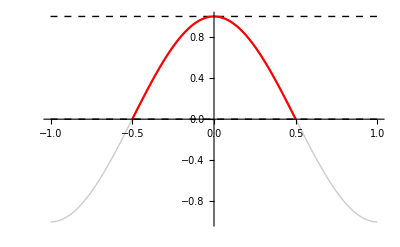

```mathematica
Show[Plot[{Cos[θ π],0,1},{θ,-1,1},PlotStyle->pltStyles[[1;;3]]],
Plot[Cos[π θ],{θ,-1/2,1/2},PlotStyle->Red]]
```